Implements Example 7.1 in Wachsmuth and Wachsmuth (2011), https://doi.org/10.1051/cocv/2010027

```mathematica
a= -30; b = 30; β = 1/2;
```

```mathematica
z[x_]:= Sin[2 Pi x]
```

```mathematica
u[x_]:= Piecewise[{{a, 1/12 < x < 5/12}, {b, 7/12 < x < 11/12}}, 0]
```

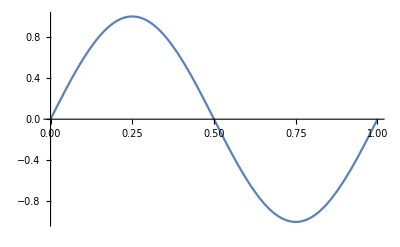

```mathematica
Plot[z[x], {x, 0, 1}]
```

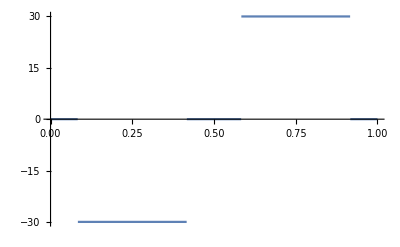

```mathematica
Plot[u[x], {x, 0, 1}]
```

```mathematica
state = DSolve[{-y''[x] == u[x], y[0] == 0, y[1]==0}, y[x], x]
```

{{y[x]→-5 x+(Piecewise[{{0, x≤1/12}, {5/48-(5 x)/2+15 x^2, 1/12<x≤5/12}, {-5/2+10 x, 5/12<x≤7/12}, {-365/48+(55 x)/2-15 x^2, 7/12<x≤11/12}, {5, True}}])}}

```mathematica
FullSimplify[%]
```

{{y[x]→Piecewise[{{5-5 x, 12 x>11}, {-5 x, 12 x≤1}, {-5/2+5 x, 5/12<x≤7/12}, {5/48 (-73+72 (3-2 x) x), 7/12<x≤11/12}, {5/48+15/2 x (-1+2 x), True}}]}}

```mathematica
statesol[x_]:=y[x]/.state[[1]]
```

```mathematica
statesol[x]
```

-5 x+(Piecewise[{{0, x≤1/12}, {5/48-(5 x)/2+15 x^2, 1/12<x≤5/12}, {-5/2+10 x, 5/12<x≤7/12}, {-365/48+(55 x)/2-15 x^2, 7/12<x≤11/12}, {5, True}}])

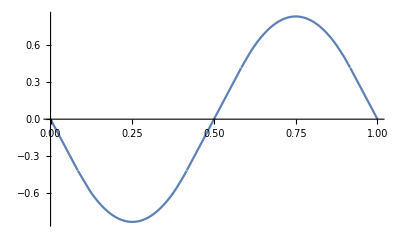

```mathematica
Plot[statesol[x],{x,0,1}]
```

```mathematica
yd[x_]:= statesol[x] + 4 Pi Pi Sin[2 Pi x]
```

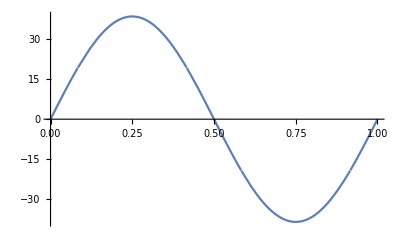

```mathematica
Plot[yd[x], {x,0,1}]
```

Optimal objective function value

```mathematica
1/2Integrate[(4 Pi Pi Sin[2 Pi x])^2 , {x,0,1}] + β/2 Integrate[  Abs[u[x]], {x,0,1}]
```

5+4 π^4

```mathematica
N[%, 20]
```

394.63636413600974895